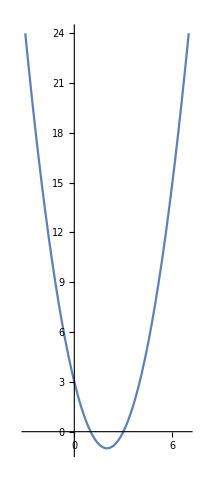

```mathematica
ParametricPlot[{t+2,t^2-1},{t,-5,5}, PlotRange->Automatic, AspectRatio->Automatic]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p1.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Homework/p1.pdf

```mathematica
p2 = ParametricPlot3D[{2Cos[t],t,2Sin[t]},{t,-2Pi,2Pi}, AxesOrigin-> {0,0,0}, AxesLabel->{x,y,z}, ViewPoint-> Dynamic[vp],Boxed->False, PlotRange->Automatic]
```

-Graphics3D-

```mathematica
vp={2,1,1};
ParametricPlot3D[{2Cos[t],2t,2Sin[t]},{t,-2Pi,2Pi},AxesLabel->{"X","Y","Z"},Axes->True,AxesEdge->{{1,0},{1,0},{1,1}},ViewPoint->Dynamic[vp],PlotLabel->Dynamic[vp], Boxed->False, AxesOrigin->{0,0,0}, PlotRange->15]
```

-Graphics3D-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p2.pdf",p2]
```

www/Teaching/Summer 2020/MAT 203/Homework/p2.pdf

```mathematica
Plot3D[Sqrt[36-x^2-y^2], {x,-6,6},{y,-6,6}, AxesLabel->{"x","y","z"},AxesEdge->{{0,1},{0,1},{0,0}}, ViewPoint->{2,1,1}, PlotStyle->Opacity[0.5], Mesh->None, Boxed->False, AxesOrigin->{0,0,0}, PlotRange->Full]
```

-Graphics3D-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p3.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Homework/p3.pdf

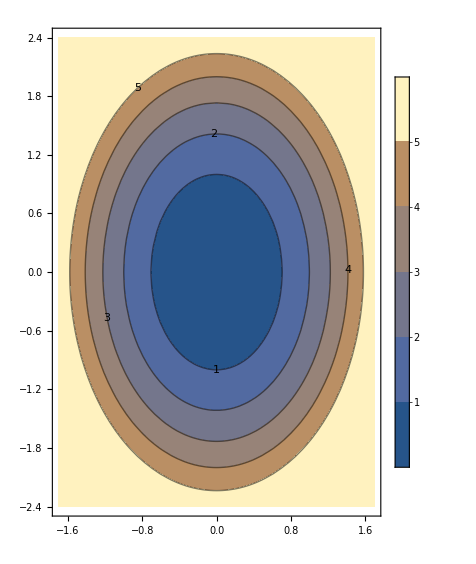

```mathematica
ContourPlot[2x^2+y^2,{x,-1.7, 1.7},{y,-2.4,2.4},
Contours-> {1.,2.,3.,4.,5.},ContourLabels->True, PlotLegends->Automatic,AspectRatio->2.4/1.7]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p4.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Homework/p4.pdf

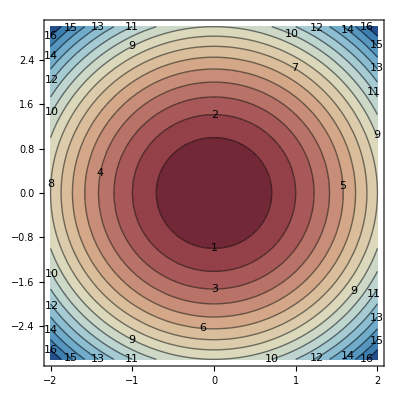

```mathematica
ContourPlot[2x^2+y^2,{x,-2,2},{y,-3,3},Contours->{1, 2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},ContourLabels-> True,PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"z-value"],ColorFunction->"RedBlueTones"]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p4.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Homework/p4.pdf

```mathematica
Plot3D[2x^2+y^2,{x,-2,2},{y,-3,3},AspectRatio->3/2]
```

-Graphics3D-

```mathematica
Plot3D[2 x^2+y^2,{x,-2,2},{y,-3,3},MeshFunctions->{#3&},ViewPoint-> Dynamic[vp]]
```

-Graphics3D-

```mathematica
Plot3D[2 x^2+y^2,{x,-2,2},{y,-3,3},Mesh->Automatic,MeshFunctions->{#3&},AxesLabel->{"x","y","z"},Axes->True,AxesEdge->{{1,0},{1,0},{0,1}},ViewPoint->{2,1,1},ColorFunction->"RedBlueTones"]
```

-Graphics3D-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p5.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Homework/p5.pdf

```mathematica
Plot3D[(x^2*y)/(x^4+y^2),{x,-.000005,.000005},{y,-.000005,.000005},AxesLabel->{"x","y","z"},Axes->True,AxesEdge->{{1,0},{1,0},{0,1}},ViewPoint->{2,1,1},ColorFunction->"RedBlueTones",PlotRange->Automatic]
```

-Graphics3D-

```mathematica
r[t_]:={Sin[t],Cos[t],t}
```

```mathematica
u[t_]:={Sin[t],Cos[t],1/t}
```

```mathematica
r[t].u[t]
```

1+Cos[t]^2+Sin[t]^2

```mathematica
Cross[r[t],u[t]]
```

{Cos[t]/t-t Cos[t],-Sin[t]/t+t Sin[t],0}

```mathematica
D[%369,t]
```

0

```mathematica
D[%370,t]
```

{-Cos[t]-Cos[t]/t^2-Sin[t]/t+t Sin[t],-Cos[t]/t+t Cos[t]+Sin[t]+Sin[t]/t^2,0}

```mathematica
%372//TeXForm
```

\left\{-\frac{\cos (t)}{t^2}+t \sin (t)-\frac{\sin (t)}{t}-\cos (t),\frac{\sin (t)}{t^2}+\sin (t)+t \cos
   (t)-\frac{\cos (t)}{t},0\right\}

```mathematica
Simplify[%372]
```

{(-(1+t^2) Cos[t]+t (-1+t^2) Sin[t])/t^2,(-1/t+t) Cos[t]+(1+1/t^2) Sin[t],0}

```mathematica
% // TeXForm
```

```mathematica
D[u[2t],t]
```

{2 Cos[2 t],-2 Sin[2 t],-1/(2 t^2)}

```mathematica
% // TeXForm
```

\left\{2 \cos (2 t),-2 \sin (2 t),-\frac{1}{2 t^2}\right\}

```mathematica
D[Sec[t],t] // TeXForm
```

\tan (t) \sec (t)

```mathematica
Integrate[Sec[t],t]
```

-Log[Cos[t/2]-Sin[t/2]]+Log[Cos[t/2]+Sin[t/2]]

```mathematica
% // TeXForm
```

\log \left(\sin \left(\frac{t}{2}\right)+\cos \left(\frac{t}{2}\right)\right)-\log \left(\cos
   \left(\frac{t}{2}\right)-\sin \left(\frac{t}{2}\right)\right)

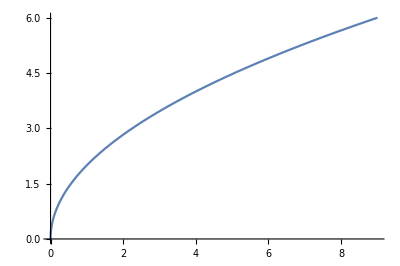

```mathematica
ParametricPlot[{t^2,2t},{t,0,3}]
```

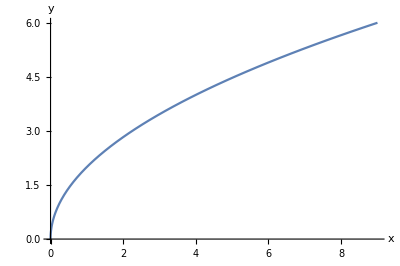

```mathematica
Show[%,AxesLabel->{"x","y"}]
```

```mathematica
2Integrate[Sqrt[t^2+1],{t,0,3}]
```

3 √10+ArcSinh[3]

```mathematica
%// TeXForm
```

3 \sqrt{10}+\sinh ^{-1}(3)

```mathematica
D[t*Sqrt[1+t^2],t]
```

t^2/(√(1+t^2))+√(1+t^2)

```mathematica
D[Log[Sqrt[1+t^2]+t],t]
```

(1+t/(√(1+t^2)))/(t+√(1+t^2))

```mathematica
%386-%387
```

t^2/(√(1+t^2))+√(1+t^2)-(1+t/(√(1+t^2)))/(t+√(1+t^2))

```mathematica
Simplify[t^2/(√(1+t^2))+√(1+t^2)-(1+t/(√(1+t^2)))/(t+√(1+t^2))]
```

(2 t^2)/(√(1+t^2))

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p6.pdf", %]
```

www/Teaching/Summer 2020/MAT 203/Homework/p6.pdf

```mathematica
Plot3D[8x+10y-0.001(x^2+x*y+y^2)-10000,{x,0,20000}, {y,0,20000}]
```

-Graphics3D-

```mathematica
Plot3D[((100-x*y)*x*y)/(2(x+y)), {x,0,10000},{y,0,10000}]
```

-Graphics3D-

```mathematica
r[t_]:={Sin[t], Cos[t], t}
```

```mathematica
u[t_]:={Sin[t], Cos[t], t^{-1}}
```

```mathematica
D[r[t],t]
```

{Cos[t],-Sin[t],1}

```mathematica
% // TeXForm
```

\{\cos (t),-\sin (t),1\}

```mathematica
D[u[t]-2r[t],t]
```

{-Cos[t],Sin[t],{-2-1/t^2}}

```mathematica
D[u[t],t]
```

{Cos[t],-Sin[t],{-1/t^2}}

```mathematica
% //TeXForm
```

\left\{\cos (t),-\sin (t),\left\{-\frac{1}{t^2}\right\}\right\}

```mathematica
%16 // TeXForm
```

\left\{-\cos (t),\sin (t),\left\{-\frac{1}{t^2}-2\right\}\right\}

```mathematica
D[3t*r[t],t]
```

{3 t Cos[t]+3 Sin[t],3 Cos[t]-3 t Sin[t],6 t}

```mathematica
% // TeXForm
```

\{3 \sin (t)+3 t \cos (t),3 \cos (t)-3 t \sin (t),6 t\}

```mathematica
D[r[t].u[t],t]
```

Dot::rect: Nonrectangular tensor encountered.

{Cos[t],-Sin[t],1}.{Sin[t],Cos[t],{1/t}}+{Sin[t],Cos[t],t}.{Cos[t],-Sin[t],{-1/t^2}}

```mathematica
r[t].u[t]
```

Dot::rect: Nonrectangular tensor encountered.

{Sin[t],Cos[t],t}.{Sin[t],Cos[t],{1/t}}

```mathematica
Flatten[u[t]]
```

{Sin[t],Cos[t],1/t}

```mathematica
u[t]=Flatten[u[t]]
```

{Sin[t],Cos[t],1/t}

```mathematica
r[t].u[t]
```

1+Cos[t]^2+Sin[t]^2

```mathematica
TrigReduce[1+Cos[t]^2+Sin[t]^2]
```

2

```mathematica
Cross[r[t],u[t]]
```

{Cos[t]/t-t Cos[t],-Sin[t]/t+t Sin[t],0}

```mathematica
D[%,t]
```

{-Cos[t]-Cos[t]/t^2-Sin[t]/t+t Sin[t],-Cos[t]/t+t Cos[t]+Sin[t]+Sin[t]/t^2,0}

```mathematica
% // TeXForm
```

\left\{-\frac{\cos (t)}{t^2}+t \sin
   (t)-\frac{\sin (t)}{t}-\cos
   (t),\frac{\sin (t)}{t^2}+\sin (t)+t \cos
   (t)-\frac{\cos (t)}{t},0\right\}

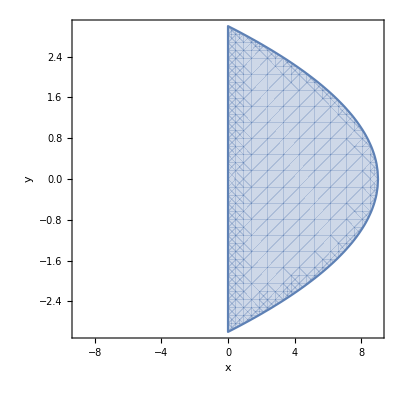

```mathematica
RegionPlot[  0 < x< 9-y^2, {x,-9, 9},{y,-3,3}, Axes->True,  AxesLabel->{"x", "y"}]
```

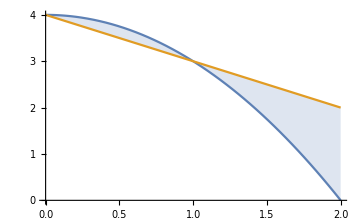

```mathematica
Plot[{4-x^2,4-x},{x,-0,2},Filling->{1->{2}}]
```

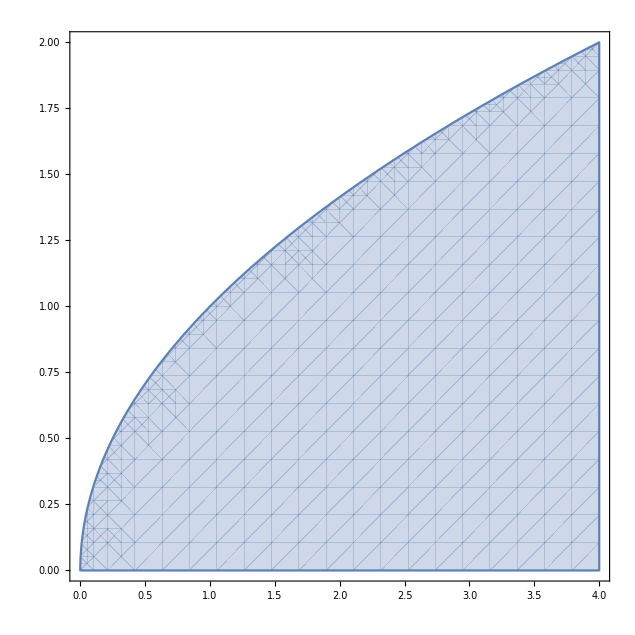

```mathematica
RegionPlot[y ≤ Sqrt[x], {x,0,4}, {y,0,2}]
```

```mathematica
Plot3D[x*y/2, {x,0,4}, {y,0,3}]
```

-Graphics3D-

```mathematica
Plot3D[(x y)/2,{x,0,4},{y,0,3}, PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
Plot3D[(x y)/2,{x,0,4},{y,0,3},Mesh->None,PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
RegionPlot3D[z≥ 0 && z≤ 1-x*y && y≥ x, {x,0,1}, {y,0,1},{z,0,1}, PlotStyle->Opacity[0.5], Mesh->None, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Plot3D[1-x*y, {x,0,1}, {y,0,1}]
```

-Graphics3D-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p7.pdf", %]
```

www/Teaching/Summer 2020/MAT 203/Homework/p7.pdf

```mathematica
Integrate[1, {x,-3,3}, {y,0,9-x^2}]
```

36

```mathematica
Integrate[2-x-y,{x,0,2},{y,0,2-x}]
```

4/3

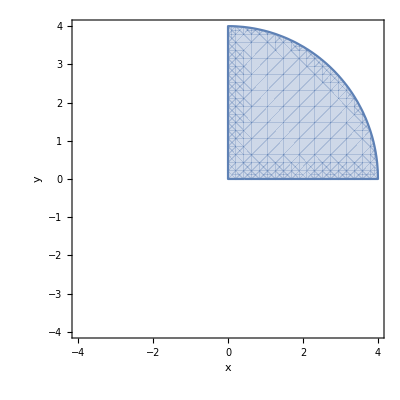

```mathematica
RegionPlot[  0 < x< Sqrt[16-y^2] && y ≥ 0, {x,-4, 4},{y,-4,4}, Axes->True,  AxesLabel->{"x", "y"}]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Homework/p8.pdf", %]
```

www/Teaching/Summer 2020/MAT 203/Homework/p8.pdf

```mathematica
Integrate[x^2+y^2, {y,0,4},{x,0,Sqrt[16-y^2]}]
```

32 π

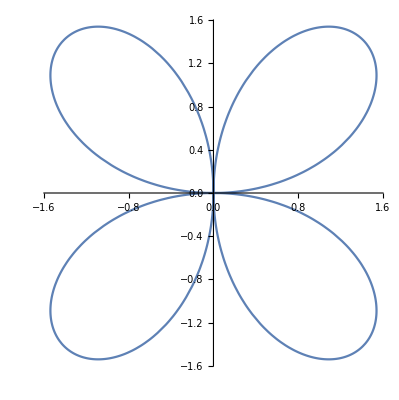

```mathematica
PolarPlot[r=2Sin[2θ],{θ,0,2π}]
```

```mathematica
ParametricPlot[{2Sin[2t]*Cos[t],2Sin[2t]*Sin[t]}, {t,0,2π}]
```

-Graphics-

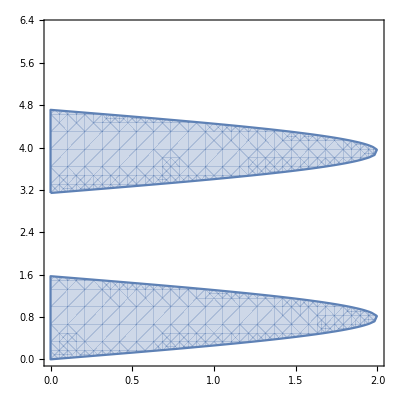

```mathematica
RegionPlot[r<2Sin[2t],{r,0,2},{t,0,2π}]
```

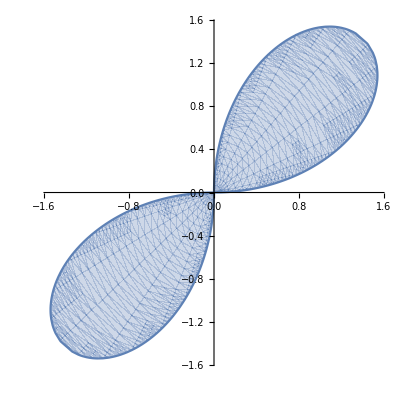

```mathematica
Show[PolarPlot[r=2Sin[2t] && r>0,{t,0,2π}],RegionPlot[0<r<2Sin[2t],{r,0,2},{t,0,2π},PlotPoints->30]/.GraphicsComplex[a_,b__]:>GraphicsComplex[#1 {Cos[#2],Sin[#2]}&@@@a,b]]
```

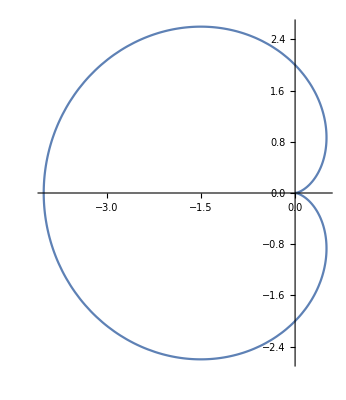

```mathematica
PolarPlot[r=2-2Cos[t],{t,0,2π}]
```

```mathematica
PolarPlot[r=2Sin[2t] ,{t,0,2π}]
```

-Graphics-

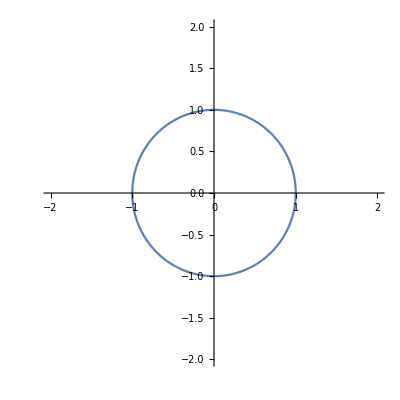

```mathematica
PolarPlot[r=1, {t,0,2π}, PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p1.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p1.pdf

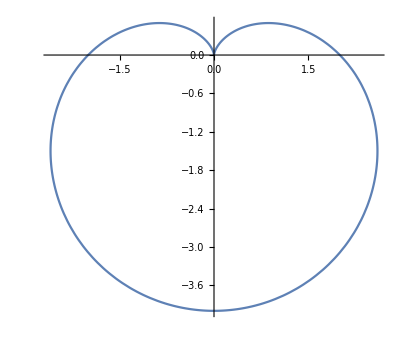

```mathematica
PolarPlot[r=2-2Sin[t],{t,0,2π}]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p2.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p2.pdf

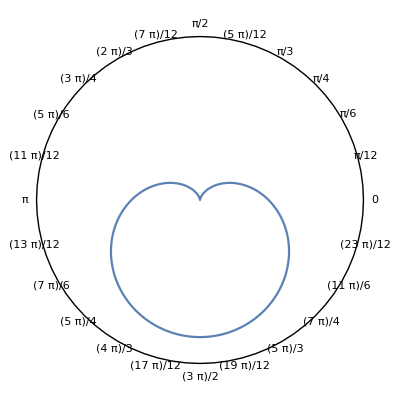

```mathematica
PolarPlot[r=2-2Sin[t],{t,0,2Pi},PolarAxes->Automatic,PolarTicks->{"Radians", Automatic}]
```

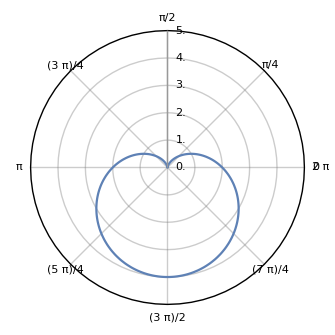

```mathematica
PolarPlot[2-2Sin[t] ,{t,0,2 Pi},PolarAxes->True,PolarGridLines->{{0,Pi/4,Pi/2,3Pi/4,Pi,5Pi/4,3 Pi/2,7Pi/4},{1,2,3,4}},PolarTicks->{Table[i,{i,0,2 Pi,Pi/4}],Table[j,{j,0,5,1}]}]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p2.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p2.pdf

```mathematica
PolarPlot[t ,{t,0,8 Pi},PolarAxes->True,PolarGridLines->{{0,Pi/4,Pi/2,3Pi/4,Pi,5Pi/4,3 Pi/2,7Pi/4},Automatic},PolarTicks->{Table[i,{i,0,2 Pi,Pi/4}],Table[j,{j,0,28,4}]}, PlotRange->{0,20},{0,2Pi}]
```

PolarPlot::nonopt: Options expected (instead of {0,2 π}) beyond position 2 in PolarPlot[t,{t,0,8 π},PolarAxes→True,PolarGridLines→{{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4},Automatic},PolarTicks→{Table[i,{i,0,2 π,π/4}],Table[j,{j,0,28,4}]},PlotRange→{0,20},{0,2 π}]. An option must be a rule or a list of rules.

```mathematica
PolarPlot[t,{t,0,8Pi},PolarGridLines->{{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4},Automatic},  PolarTicks->{"Radians",Automatic}]
```

-Graphics-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p3.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p3.pdf

```mathematica
PolarPlot[Sin[2θ],{θ,0,2π},PolarGridLines-> True,RegionFunction->Function[{x,y,θ,r},r>0]]
```

-Graphics-

```mathematica
PolarPlot[Sin[2θ],{θ,0,2Pi}, PolarGridLines->True]
```

-Graphics-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p4.pdf",%196]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p4.pdf

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p5.pdf",%197]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p5.pdf

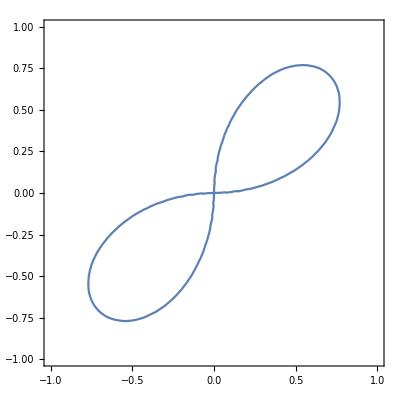

```mathematica
ContourPlot[(x^2+y^2)^{3/2}== (2x*y), {x,-1,1},{y,-1,1}, Axes->True]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p6.pdf",%204]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p6.pdf

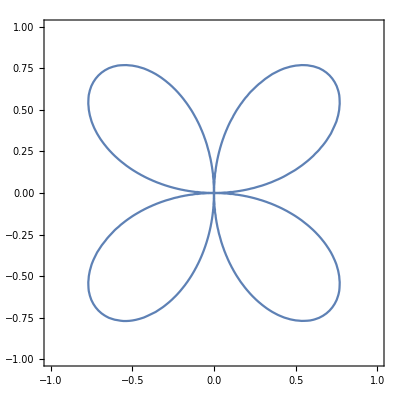

```mathematica
ContourPlot[(x^2+y^2)^{3/2}== Abs[2x*y], {x,-1,1},{y,-1,1}, Axes->True]
```

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p7.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Lecture slides/polar_p7.pdf

```mathematica
ContourPlot3D[{x^2+y^2+z^2== 4, z^2== 3x^2+3y^2}, {x,-2,2}, {y,-2,2}, {z,-2,2}, ContourStyle-> Opacity[0.5], Mesh->None, ViewPoint->Above]
```

-Graphics3D-

```mathematica
ContourPlot3D[{x^2+y^2+z^2== 1, z== 1/2}, {x,-1,1}, {y,-1,1}, {z,-1,1}, ContourStyle-> Opacity[0.5], Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[{z== 8-x^2-y^2, z== x^2+y^2}, {x,-3,3}, {y,-3,3}, {z,-8,8}, ContourStyle-> Opacity[0.5], Mesh->None, ViewPoint->Above]
```

-Graphics3D-

```mathematica
ContourPlot3D[{z== 8-x^2-y^2, z== x^2+y^2}, {x,-5,5}, {y,-5,5}, {z,-10,10}, ContourStyle-> Opacity[0.5], Mesh->None, ViewPoint->Above]
```

-Graphics3D-

```mathematica
ContourPlot3D[{x^2+y^2+z^2== 8,z== 2}, {x,-4,4}, {y,-4,4}, {z,-4,4}, ContourStyle-> Opacity[0.5], Mesh->None, Axes->True, AxesOrigin->{0,0,0}, Boxed->False]
```

-Graphics3D-

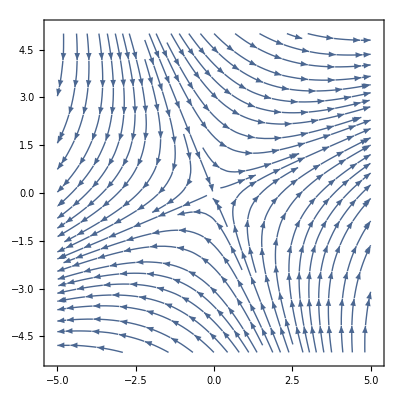

```mathematica
StreamPlot[{x+y,x-y},{x,-5,5},{y,-5,5}]
```

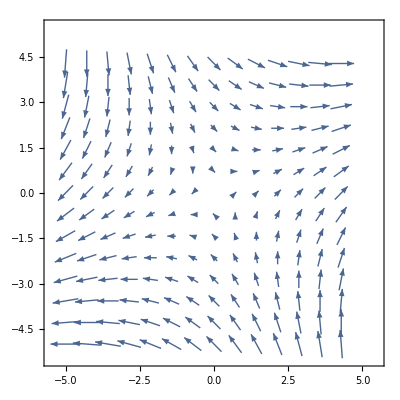

```mathematica
VectorPlot[{x+y,x-y},{x,-5,5},{y,-5,5}]
```

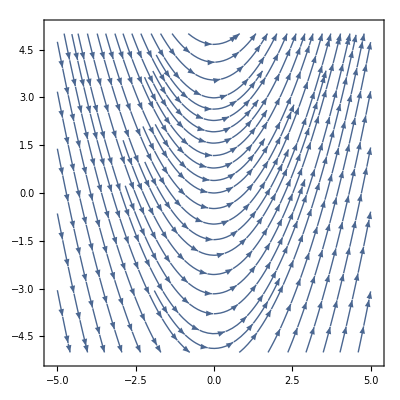

```mathematica
StreamPlot[{1,x},{x,-5,5},{y,-5,5}]
```

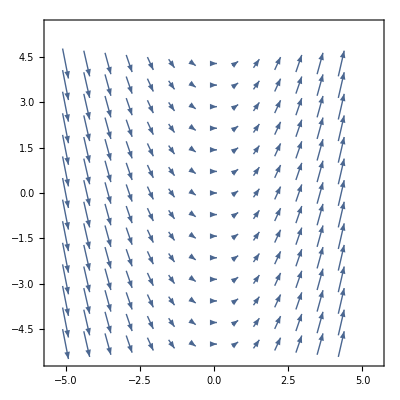

```mathematica
VectorPlot[{1,x},{x,-5,5},{y,-5,5}]
```

```mathematica
VectorPlot3D[{1,1,z},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
VectorPlot3D[{x+y,y+z,z+x},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
RegionPlot3D[x ≥ -1 && x≤ 1 && y≥ -Sqrt[1-x^2] && y ≤ Sqrt[1-x^2] && z≥ 1 && z≤ 1+Sqrt[1-x^2-y^2],{x,-1,1}, {y,-1,1},{z,0,4}, PlotStyle->Opacity[0.5], Mesh->None, AxesLabel->{"x","y","z"}, ViewPoint->{3,2,1} ]
```

-Graphics3D-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Exams/p1.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Exams/p1.pdf

```mathematica
Integrate[(x^2+2y), {x,0,2}, {y,x^2,2x}]
```

88/15

```mathematica
RegionPlot3D[x ≥ 0 && x≤ 3 && y≥ 0 && y ≤ Sqrt[9-x^2] && z≥ 0 && z≤ Sqrt[9-x^2-y^2],{x,0,4}, {y,0,4},{z,0,4}, PlotStyle->Opacity[0.5], Mesh->None, AxesLabel->{"x","y","z"}, ViewPoint->{3,2,1} ]
```

-Graphics3D-

```mathematica
Export["www/Teaching/Summer 2020/MAT 203/Exams/p5.pdf",%]
```

www/Teaching/Summer 2020/MAT 203/Exams/p5.pdf

```mathematica
Integrate[r,{θ,0,2Pi},{r,1,2+Cos[θ]}]
```

(7 π)/2

```mathematica
Integrate[x^2Sqrt[1-x^2],x]
```

1/8 (x √(1-x^2) (-1+2 x^2)+ArcSin[x])

```mathematica
% // TeXForm
```

\frac{1}{8} \left(x \sqrt{1-x^2} \left(2 x^2-1\right)+\sin ^{-1}(x)\right)

```mathematica
%5 // x-> 1
```

(x→1)[1/8 (x √(1-x^2) (-1+2 x^2)+ArcSin[x])]

```mathematica
%5 /. x-> 1
```

π/16

```mathematica
%5/. x-> 0
```

0

```mathematica
Integrate[x*r^2, {x,1,1+Sqrt[1-r^2]}]
```

r^2 (-1/2+1/2 (1+√(1-r^2))^2)

```mathematica
Simplify[%]
```

1/2 r^2 (1-r^2+2 √(1-r^2))

```mathematica
%12 // TeXForm
```

r^2 \left(\frac{1}{2} \left(\sqrt{1-r^2}+1\right)^2-\frac{1}{2}\right)

```mathematica
%13 // TeXForm
```

\frac{1}{2} r^2 \left(-r^2+2 \sqrt{1-r^2}+1\right)

```mathematica
Integrate[%13,r]
```

1/2 (-r^5/5-1/4 r √(1-r^2)+1/6 r^3 (2+3 √(1-r^2))+ArcSin[r]/4)

```mathematica
Simplify[%]
```

-r^5/10-1/8 r √(1-r^2)+1/12 r^3 (2+3 √(1-r^2))+ArcSin[r]/8

```mathematica
% // TeXForm
```

-\frac{r^5}{10}-\frac{1}{8} \sqrt{1-r^2} r+\frac{1}{12} \left(3 \sqrt{1-r^2}+2\right) r^3+\frac{1}{8} \sin ^{-1}(r)

```mathematica
%17 /. r-> 1
```

1/15+π/16

```mathematica
%17 /. r->0
```

0

```mathematica
BinomialDistribution[1000,0.0018]
```

BinomialDistribution[1000,0.0018]

```mathematica
DiscretePlot[%,1000]
```

DiscretePlot::pllim: Range specification 1000 is not of the form {x, xmin, xmax}.

DiscretePlot[%,1000]

```mathematica
DiscretePlot[%21, {x,0,1000}]
```

-Graphics-

```mathematica
PDF[BinomialDistribution[1000,0.0018],x]
```

Piecewise[{{0.0018^x 0.9982^(1000-x) Binomial[1000,x], 0≤x≤1000}, {0, True}}]

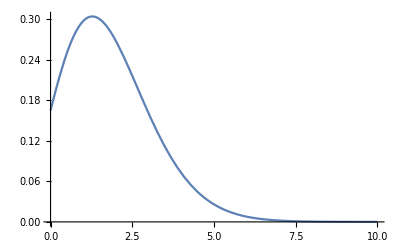

```mathematica
Plot[%25,{x,0,10}]
```

```mathematica
CDF[BinomialDistribution[1000,0.0018],x]
```

Piecewise[{{BetaRegularized[0.0018,1,1+Floor[x],1000-Floor[x]], 0≤x<1000}, {1, x≥1000}, {0, True}}]

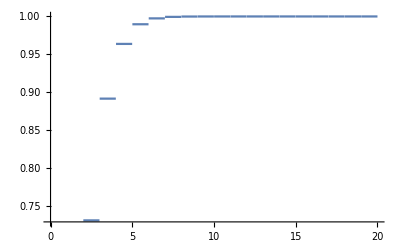

```mathematica
Plot[%27,{x,0,20}]
```